```mathematica
list = Import[NotebookDirectory[]<>"/res/out_0.0.txt","Table"];
Length[list]
len=Length[list[[1]]]
```

10

100

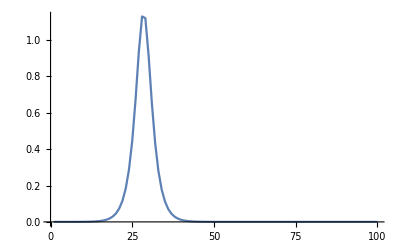

```mathematica
ListLinePlot[-list[[2]],PlotRange->All]
```

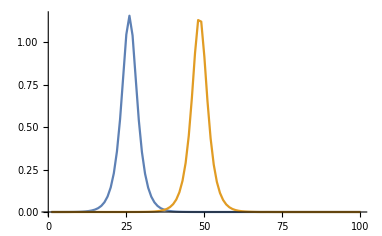

```mathematica
ListLinePlot[{-list[[1]],-list[[-1]]},PlotRange->Full]
```

```mathematica
f1=NIntegrate[Interpolation[list[[1]]^2,InterpolationOrder->2][x],{x,1,len-1}]
f2=NIntegrate[Interpolation[list[[-1]]^2,InterpolationOrder->2][x],{x,1,len-1}]
(f2-f1)/f1
```

27.1576

27.1581

0.0000190716

```mathematica
list1 = Import[NotebookDirectory[]<>"/res/out_0.0.txt","Table"];
```

```mathematica
max=Max[Map[Max,-list1]];
min=Min[Map[Min,-list1]];
Manipulate[
l1=-list1[[n]] + list1[[n,1]];
ListLinePlot[{l1},PlotRange->{0,2}],
{n,1,Length[list1],1}]
```